```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\HILL\Documents\GitHub\thesis\figures\spectro

```mathematica
data=Import["raw_data.csv","Dataset",HeaderLines->1];
```

```mathematica
r=Normal[data[All,"x"]];
n=Normal[data[All,"y"]];
err=Normal[data[All,"err"]];
```

```mathematica
parabola=
ReplaceAll[p0*x^2+p1*x+p2,{p0->0.0001261,p1->-0.002145,p2->0.4325}];
```

```mathematica
l=0.03 (* Ticks Length *);
```

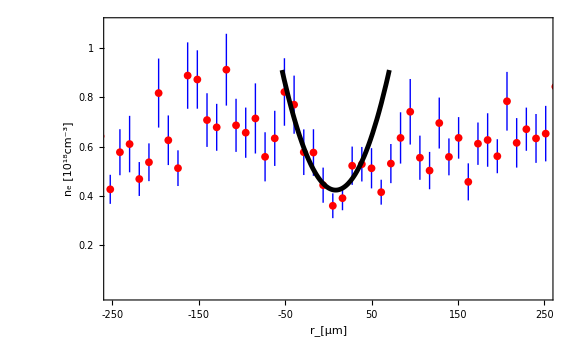

```mathematica
parabolic=Show[
{ListPlot[
Thread[{r,MapThread[Around,{n,err}]}],
IntervalMarkers->"Fences",
IntervalMarkersStyle->{Thick,Blue},
PlotMarkers->{Automatic, 8},
PlotStyle->Red
],
Plot[parabola,{x,-250,250},PlotStyle->Directive[Thickness->0.006,Black],PlotRange->{0,0.91}]
},
PlotRange->{{-250,250},{0,1.1}},
FrameTicks->{
Table[{50j,50j,l,Directive[Thick]},{j,-5,5,1}]
, Table[{j,j,l,Directive[Thick]},{j,0.2,1.2,0.2}]/. 1.->1
}
,
FrameTicksStyle->Directive[Black,FontSize->20,FontFamily->"Latin Modern Roman 10",Thick],
AxesStyle->{{Black,Thick},{Black,Thick}},
AxesLabel->{Style["r_[µm]"(* Subscript[r,][µm] *),FontFamily->"Latin Modern Roman 10",Large],Style["n_e [10^18cm^-3]",FontFamily->"Latin Modern Roman 10",Large]},
ImageSize->Large,
Frame->{True,True,False,False}
]
```

```mathematica
Export["parabolic.pdf",parabolic]
```

parabolic.pdf

x axis label: Capillary radius, [um]
y axis label: Plasma Density, [10^18 cm^(-3)]

```mathematica
Plot[0.015 x^2,{x,-10,10},Ticks->{Automatic,Table[j,{j,0,1.2,0.2}]/.1.->1}]
```

```mathematica
Table[j,{j,0,1.2,0.2}]
```

{0.,0.2,0.4,0.6,0.8,1,1.2}